## 二型全息图

使用二型全息图

## 自动计算的部分

```mathematica
(*该部分每次仅运行一次*)
<<Notation`
Symbolize[Subscript[w, 0]]
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
Notation[|ℓ_| ⟺ Abs[ℓ_]]
Notation[Subscript[L, 𝓅_]^ℓ_[x_] ⟺ LaguerreL[𝓅_,|ℓ_|,x_]]
Notation[Subscript[d, k_,l_]^j_[β_] ⟺ WignerD[{j_,k_,l_},β_]]
Subscript[w, 0]=1;
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=Numerator[Rationalize@Ω];
Q=Denominator[Rationalize@Ω];
(*输入整数p*)
p=-1;
SetDirectory[NotebookDirectory[]];
(*定义带几何相（红色背景）的SU2的相干光的表达式*)
A[x_,y_,α_,β_,γ_,m_,n_,M_,Θ_]:= 2^(-M/2) ∑_(K=0)^M ⅇ^(ⅈ K (γ)+ⅈ (-6 K+m-n) Θ) √Binomial[M,K] Sum[(1/(√π))ⅈ^(-10 K-2 n+µ-|µ|) ⅇ^(-x^2-y^2-(ⅈ α µ)/2+ⅈ µ Arg[x+ⅈ y]) (x^2+y^2)^((|µ|)/2) √((2^(1+|µ|) ((1/2) (4 K+m+n-|µ|))!)/((1/2) (4 K+m+n+|µ|))!) (Subscript[L, 1/2 (4 K+m+n-|µ|)]^µ)[2 (x^2+y^2)] (Subscript[d, µ/2,1/2 (-6 K+m-n)]^(1/2 (4 K+m+n)))[β],{µ,-4 K-m-n,4 K+m+n,2}]
𝕀[x_,y_,α_,β_,γ_,m_,n_,M_,Θ_]:=A[x,y,α,β,γ,m,n,M,Θ](A[x,y,α,β,γ,m,n,M,Θ])*
𝒫[x_,y_,α_,β_,γ_,m_,n_,M_,Θ_]:=Arg[A[x,y,-α/3,β,γ,m,n,M,Θ]]
```

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[w, 0]]
Symbolize[Subscript[z, R]]
```

```mathematica
dx
```

```mathematica
dx=(2*6*Subscript[w, 0])/200;
δ=3;

𝒶[x_,y_,α_,β_,γ_,m_,n_,M_,Θ_]:=Abs[𝕀[x,y,α,β,γ,m,n,M,Θ]]/4.6
f[𝒶_]:=InverseFunction[ConditionalExpression[BesselJ[0,#],0≤#≤ 2.40483]&][𝒶]
Hol[]:=Arg[Exp[ⅈ(𝒫[x,y,α,β,γ,m,n,M,Θ]+2π x/(δ dx))]]
```

```mathematica
Exp[ⅈ(f[𝒶[x,y,α,β,γ,m,n,M,Θ]]Sin[𝒫[x,y,α,β,γ,m,n,M,Θ]+2π x/(δ dx)])]
```

## 用相位透射型编码复振幅

相位透射函数型+计算全息
用相位型CGH的透射系数创建相位函数，以对复振幅场进行编码。

产生任意的复振幅光场，其振幅和相位调制独立确定，该复振幅场可表示为

其中，振幅，，。

通常，编码任意复振幅场的，其复振幅透射系数为的子集。

对于相位型，该子集由单位模复数点构成。

```mathematica
Table[Norm[Exp[ⅈ a]],{a,-10,10}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

相位型的透射系数，可表示为被编码场的振幅和相位的函数

:CGH phase modulation/CGH的相位调制函数
：complex modulation复振幅调制函数/signal信号

为何谈相位？

所谓的相位型，即相位透射型：phase transmittance CGH

对相位型CGH的透射系数在域的傅级数，确定全息图的相位调制函数。

1. 将CGH透射系数表示为

注：对于积分式，由于是对进行积分，则只是振幅的函数。

若对于正数恒等式成立，则信号从级数展开式的1阶项恢复。

信号编码条件成立的充要条件是

注：最大值为，故编码条件成立中，则相位调制函数的效率受到限制。

接下来只讨论奇对称CGH相位调制函数

```mathematica
Exp[ⅈ ϕ]A α  ==Exp[ⅈ ψ[α,ϕ]]
```

A ⅇ^(ⅈ ϕ) α==ⅇ^(ⅈ ψ[α,ϕ])

#### 1. 1型相位CGF

全息图的相位调制函数为，该相位型的傅系数为，其中定义为。则，可从求出

```mathematica
Sinc[x]//FunctionExpand
```

Sin[x]/x

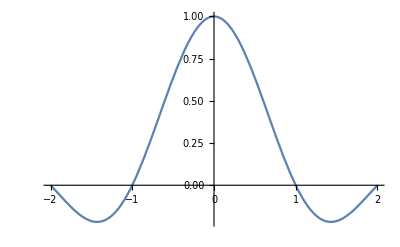

```mathematica
Plot[Sin[Pi x]/(Pi x),{x,-2,2}]
Solve[Sin[Pi(1-f[α])]/(Pi (1-f[α]))==α,]
```

```mathematica
MaTeX["sinc(1-f(\\alpha))=\\alpha"]//CopyToClipboard[ExpressionCell[#,"Print"]]&
```

-Graphics-

```mathematica
"\\int_{-\\pi}^{\\pi} \\sin [\\psi(\\phi, a)-\\phi] \\mathrm{d} \\phi&=0 \\\\"=="\\int_{-\\pi}^{\\pi} \\sin [\\psi(\\phi, a)-\\phi] \\mathrm{d} \\phi&=0 \\\\"
```

True